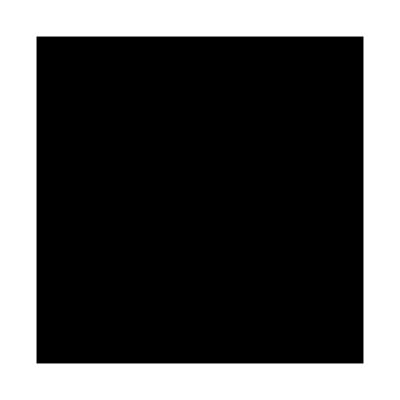

```mathematica
(*Exercício 1*)
(*começo definindo a figura geométrica*)
quadrado={{0.,0.},{0.,1.},{1.,1.},{1.,0.}}; 
Graphics[Polygon[quadrado]]
```

```mathematica
(*Defino a função responsável por gerar o espaço central*)
```

```mathematica
criaErupcao[q_]:=Module[{q1,q2,q3,q4,q5,q6,q7,q8},
q1:={
0(q[[2]]-q[[1]])+0(q[[4]]-q[[1]]),
(1/3)(q[[2]]-q[[1]]),
(1/3)(q[[2]]-q[[1]])+(1/3)(q[[4]]-q[[1]]),
(1/3)(q[[4]]-q[[1]])
};
q2:={
(1/3)(q[[2]]-q[[1]]),
(2/3)(q[[2]]-q[[1]]),
(2/3)(q[[2]]-q[[1]])+(1/3)(q[[4]]-q[[1]]),
(1/3)(q[[2]]-q[[1]])+(1/3)(q[[4]]-q[[1]])
};
q3:={
(2/3)(q[[2]]-q[[1]]),
(q[[2]]-q[[1]]),
(q[[2]]-q[[1]])+(1/3)(q[[4]]-q[[1]]),
(2/3)(q[[2]]-q[[1]])+(1/3)(q[[4]]-q[[1]])
};
q4:={
(2/3)(q[[2]]-q[[1]])+(1/3)(q[[4]]-q[[1]]),
(q[[2]]-q[[1]])+(1/3)(q[[4]]-q[[1]]),
(q[[2]]-q[[1]])+(2/3)(q[[4]]-q[[1]]),
(2/3)(q[[2]]-q[[1]])+(2/3)(q[[4]]-q[[1]])
};
q5:={
(1/3)(q[[4]]-q[[1]]),
(1/3)(q[[2]]-q[[1]])+(1/3)(q[[4]]-q[[1]]),
(1/3)(q[[2]]-q[[1]])+(2/3)(q[[4]]-q[[1]]),
(2/3)(q[[4]]-q[[1]])
};
q6:={
(2/3)(q[[2]]-q[[1]])+(2/3)(q[[4]]-q[[1]]),
(q[[2]]-q[[1]])+(2/3)(q[[4]]-q[[1]]),
(q[[2]]-q[[1]])+(q[[4]]-q[[1]]),
(2/3)(q[[2]]-q[[1]])+(q[[4]]-q[[1]])
};
q7:={
(1/3)(q[[2]]-q[[1]])+(2/3)(q[[4]]-q[[1]]),
(2/3)(q[[2]]-q[[1]])+(2/3)(q[[4]]-q[[1]]),
(2/3)(q[[2]]-q[[1]])+(q[[4]]-q[[1]]),
(1/3)(q[[2]]-q[[1]])+(q[[4]]-q[[1]])
};
q8:={
(2/3)(q[[4]]-q[[1]]),
(1/3)(q[[2]]-q[[1]])+(2/3)(q[[4]]-q[[1]]),
(1/3)(q[[2]]-q[[1]])+(q[[4]]-q[[1]]),
(q[[4]]-q[[1]])
};
{q1,q2,q3,q4,q5,q6,q7,q8}
];
```

```mathematica
criaErupcao[quadrado]
```

{{{0.,0.},{0.,0.333333},{0.333333,0.333333},{0.333333,0.}},{{0.,0.333333},{0.,0.666667},{0.333333,0.666667},{0.333333,0.333333}},{{0.,0.666667},{0.,1.},{0.333333,1.},{0.333333,0.666667}},{{0.333333,0.666667},{0.333333,1.},{0.666667,1.},{0.666667,0.666667}},{{0.333333,0.},{0.333333,0.333333},{0.666667,0.333333},{0.666667,0.}},{{0.666667,0.666667},{0.666667,1.},{1.,1.},{1.,0.666667}},{{0.666667,0.333333},{0.666667,0.666667},{1.,0.666667},{1.,0.333333}},{{0.666667,0.},{0.666667,0.333333},{1.,0.333333},{1.,0.}}}

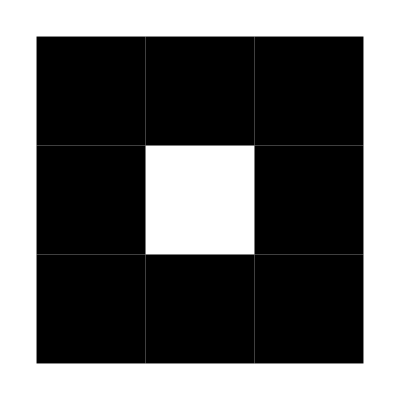

```mathematica
Graphics[Polygon/@criaErupcao[quadrado]]
```

```mathematica
(*Defino funções de iteração para automatização do processo*)
```

```mathematica
listainicial={quadrado};
itera[lista_]:=Flatten[criaErupcao/@lista,1]
listafinal[n_]:=Nest[itera,listainicial,n]
```

```mathematica
Show[Graphics[Polygon/@listafinal[6]]]
```

-Graphics-

```mathematica
(*Exercício 2*)
```

```mathematica
(*Defino uma função para tratar o conjunto de multibrot*)
```

```mathematica
multibrot:=Compile[{cx,cy,d,nmax},
Module[{z=0.+I*0.,n=0}, (* z é "declarado" como complexo *)
(
While[Abs[z]≤2 && n≤nmax, 
(
z=z^d+cx+I*cy;
n++
)
];
n
)
]
]
```

```mathematica
optam={ImageSize-> Large,LabelStyle-> {"Large"}};
```

```mathematica
(*No caso d=2 esperamos recobrar o comportamento típico do cojunto de mandelbrot. Faço um teste de validação.*)
DensityPlot[multibrot[x,y,2,200],{x,-2,0.6},{y,-1.3,1.3},PlotPoints->200,Evaluate[optam],PlotLegends->Automatic,ScalingFunctions-> "Log"]
```

-Graphics-

```mathematica
(*Justamente conforme esperado, obtivemos perfeitamente o comportamento do conjunto de mandelbrot*)
```

```mathematica
(*Verifico agora se o comportamento fractal ainda se manifesta para algum valor de d>2*)
DensityPlot[multibrot[x,y,4.67,200],{x,-2,0.6},{y,-1.3,1.3},PlotPoints->200,Evaluate[optam],PlotLegends->Automatic,ScalingFunctions-> "Log"]
```

-Graphics-

```mathematica
(*À primeira vista o comportamento do conjunto é fractal. Aproximo o gráfico em alguma determinada região para uma verificação mais refinada.*)
```

```mathematica
DensityPlot[multibrot[x,y,4.67,200],{x,-1.1,-0.9},{y,0.4,0.6},PlotPoints->200,Evaluate[optam],PlotLegends->Automatic,ScalingFunctions-> "Log"]
```

-Graphics-

```mathematica
DensityPlot[multibrot[x,y,4.67,1000],{x,-1.03,-1.00},{y,0.40,0.43},PlotPoints->300,Evaluate[optam],PlotLegends->Automatic,ScalingFunctions-> "Log"]
```

-Graphics-

```mathematica
DensityPlot[multibrot[x,y,4.67,500],{x,-1.020,-1.015},{y,0.4,0.41},PlotPoints->300,Evaluate[optam],PlotLegends->Automatic,ScalingFunctions-> "Log"]
```

-Graphics-

```mathematica
(*Concluimos que, de fato, o conjunto de multibrot ainda apresenta características fractais.*)
```